```mathematica
SOI=Import["/users/pp/git/context/Mathematica/SOIM/data/soi.txt", "table"];
TSID=Import["/users/pp/git/context/Mathematica/SOIM/data/tsi.txt", "table"];
QBO=Import["/users/pp/git/context/Mathematica/SOIM/data/qbo20.txt", "table"];
QBO70=Import["/users/pp/git/context/Mathematica/SOIM/data/qbo.txt", "table"];
CW=Import["/users/pp/git/context/Mathematica/SOIM/data/cw.txt", "table"];
CW1=Import["/users/pp/git/context/Mathematica/SOIM/data/cw1_1930.txt", "table"];
CW0=Import["/users/pp/git/context/Mathematica/SOIM/data/cw1.txt", "table"];
NINO34=Import["/users/pp/git/context/Mathematica/SOIM/data/nino34ke.txt", "table"];
tahiti=Import["/users/pp/git/context/Mathematica/SOIM/data/tahiti.txt", "table"];
darwin=Import["/users/pp/git/context/Mathematica/SOIM/data/darwin0.txt", "table"];
```

{char t,7.24073,0.146791, Years from,1880.17,to,1980.25,CC,70.9853,70.9555,-0.0298237}

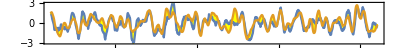

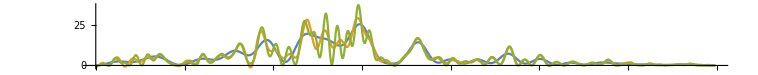

2.24721

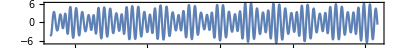

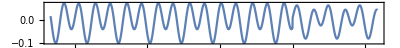

6.46418

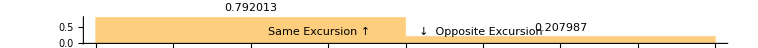

```mathematica
(* -------------------------------------------------------------- GOOD ------------------------------------------------- *)
WinHiFilter = 6;  (* 8 *)
QB=2.695; qbo[x_] :=  Cos[QB*(x+0.24*Sin[0.524*x+2.85]-0.05*Sin[0.123*x+0.13])+1.45] ; 
tsi[x_]=Cos[2*Pi/10.6*x];
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
STRT=2; STRTY=1880+STRT/12; SEP=0.0; LNGTH=1203; ENDY=1880+LNGTH/12; 
SOIT = Table[{1880+i/12, -R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 0.753;  dilate[x_] := -(0.03*Cos[2*Pi*x-0.89]);
OSC := 9.3;     TR=52.0;  CWF := 0.757;  CWR := 6.485;
Hill[x_] := CF*(1-0.19*Cos[CWF*x-.08/CWF]+0.0001*x);
Osc[x_] := -1.6*(0.03*Cos[2*Pi/OSC*x+4.3] +0.055*Cos[2*Pi/(2*OSC)*x+0.2] - 0.051*Cos[2*Pi*x/(3.0*OSC)-0.6] +.04*Cos[2*Pi*x/(6.0*OSC)-3.9]);
QBOG[x_]:=7.0*qbo[x+0.252]+0.013*Cos[2*Pi*x/(7.0)+0.1]+3.46*Cos[2*Pi*x/(2.33391)-1.51] -1.2*Cos[2*Pi*x/(1.952)-0.98] + 0.32*Cos[2*Pi*x/(2.9)-0.3];
CWG[x_]:=If[x<100, 0.07*Cos[2*Pi*x/(CWR)+1.0], 0.052*Cos[2*Pi*x/(CWR)+1.7] ] +0.03*Cos[2*Pi*x/(2*CWR)+2.1];
QTO[x_]:= 0.42*Cos[2*Pi*x/(3.801)-1] ;
RHS[x_] :=  0.93*QBOG[x]*(1+0.05*tsi[x-6.8])+CWG[x]+QTO[x]+Osc[x+1.2]+ 0.041*Cos[2*Pi*x/(18.0)-0.3];  
SOLN=NDSolve[{y''[x]+Hill[x]*y[x]+0.12*(y[x])^2 == 1*RHS[x] ,        y'[TR]==0.0, y[TR]==0.1}, y, {x, 0, 260}];   
SOIM=Table[{1880.0+x, -1.01*qbo[x+1.03]+First[-2.17*y[x+dilate[x]+0.67] /. SOLN]},{x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-3,3+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.1]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];  
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,400,1200,400}],{ω,0,π/9},PlotRange->All,AspectRatio->0.1]
2*Pi/0.233/12
 RHST = Table[{1880.0+x, RHS[x]},{x,1/12,135.0, 1/12}]; 
ListLinePlot[{Table[{1880.0+x, RHS[x]},{x,1/12,135.0, 1/12}]}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"RHS"}]
ListLinePlot[{Table[{1880.0+x, CWG[x]},{x,1/12,135.0, 1/12}]}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"Osc", "QBO"}]
2*Pi/0.081/12
SBIN = Abs[Sign[SOIT[[All,2]]]- Sign[SOIM[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
```

1.50459

{char t,7.24073,0.570328, Years from,1880.17,to,1980.25,CC,53.3383,70.9555,58.7823,-12.1732}

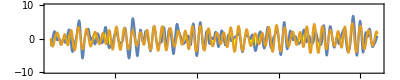

```mathematica
Window1 = 9;  
R = GaussianFilter[GaussianFilter[(1*GaussianFilter[darwin[[All,2]],Window1-0])-(1*GaussianFilter[tahiti[[All,2]],Window1-0]),Window1-2],Window1-4];
lhs=Table[{1880.0+x,  12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])-Hill[x]*R[[x*12]]  },{x,STRT/12,LNGTH/12+0, 1/12}];     
rhs=Table[{1880.0+x, -0.7*RHS[x+0.69]},  {x,STRT/12,LNGTH/12+0, 1/12}];     
SBIN = Abs[Sign[lhs[[All,2]]]- Sign[rhs[[All,2]]]]/2; 
2*Pi/.348/12
OldCC = NewCC; NewCC = 50*(1.0-N[Total[SBIN]/Length[SBIN]]) + 50*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
CC = 100*Correlation[lhs,rhs][[2,2]];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",CC, OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-10,10},Frame->True,Axes->True, Filling->{1->{{2},Yellow}}, PlotLegends->{"LHS","RHS"},AspectRatio->0.2] 
(* missing qbo *)
```

76.0075

{0.,106.627}

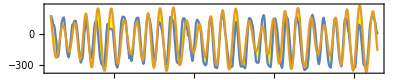

```mathematica
QBOM = Table[{1953.0+x, -47*QBOG[72.62+x]-50},{x,1/12,61.25+1/12, 1/12}];  Q = MeanFilter[QBO[[All,2]],3];
QBOT = Table[{QBOM[[i,1]], Q[[i]]},{i,1,12*61.25+1, 1}];        
100*Correlation[QBOT,QBOM][[2,2]]
Variance[QBOT]-Variance[QBOM]
ListLinePlot[{QBOT, QBOM}, AspectRatio->0.2, Filling->{1->{{2},Yellow}}, Frame->True, Axes->False, PlotLegends->{"QBO", "Model"}]
```